```mathematica
ClearAll[b,x,u0,s0,S,U];
(*======= Liberia ========*)
data = {5374,5382,5389,5421,5468,5514,5561,5607,5620,5632,5654,5676,5698,5720,5743,5763,5782,5837,5892,5946,5946,5946,5960,5985,5992,6000,6007,6007,6007,6091,6091,6139,6188,6236,6236,6236,6367,6367,6398,6430,6461,6461,6469,6469,6469,6486,6504,6521,6521,6533,6533,6533,6551,6569,6587,6614,6614,6614,6638,6638,6638,6638,6638,6665,6683,6683,6695,6706,6718,6740,6740,6772,6772,6772,6772,6772,6824,6824,6838,6838,6841,6845,6848,6882,6889,6889}
ϵ=Sum[(data[[i+1]]-data[[i]]-x*(n-data[[i]])*data[[i]]/3441790)^2,{i,Length@data-1}]
N@Minimize[ϵ,x]

n=3441790;
u= DSolve[{U'[t]==x*(n-U[t])*U[t]/n,U[0]==5374},{U[t]},t]
```

{42642.6,{x→0.00273851}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{U[t]→(9248089730 ⅇ^(t x))/(1718208+2687 ⅇ^(t x))}}

```mathematica
ClearAll[U]
U[t_]:=(9248089730 *E^(0.002738514018463815t ))/(1718208+2687 *E^(0.002738514018463815t ))
For[i=0,i<86,i++,Print[U[i]]]
```

```mathematica
N@Correlation[{5374,5382,5389,5421,5468,5514,5561,5607,5620,5632,5654,5676,5698,5720,5743,5763,5782,5837,5892,5946,5946,5946,5960,5985,5992,6000,6007,6007,6007,6091,6091,6139,6188,6236,6236,6236,6367,6367,6398,6430,6461,6461,6469,6469,6469,6486,6504,6521,6521,6533,6533,6533,6551,6569,6587,6614,6614,6614,6638,6638,6638,6638,6638,6665,6683,6683,6695,6706,6718,6740,6740,6772,6772,6772,6772,6772,6824,6824,6838,6838,6841,6845,6848,6882,6889,6889},{5374,5389,5403,5418,5433,5448,5463,5478,5493,5508,5523,5538,5553,5568,5584,5599,5614,5630,5645,5661,5676,5692,5707,5723,5738,5754,5770,5786,5802,5817,5833,5849,5865,5881,5898,5914,5930,5946,5962,5979,5995,6011,6028,6044,6061,6078,6094,6111,6128,6144,6161,6178,6195,6212,6229,6246,6263,6280,6297,6315,6332,6349,6367,6384,6402,6419,6437,6454,6472,6490,6507,6525,6543,6561,6579,6597,6615,6633,6651,6669,6688,6706,6724,6743,6761,6780}]
```

0.967782

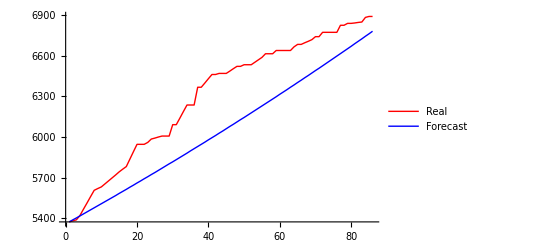

```mathematica
ListLinePlot[{{5374,5382,5389,5421,5468,5514,5561,5607,5620,5632,5654,5676,5698,5720,5743,5763,5782,5837,5892,5946,5946,5946,5960,5985,5992,6000,6007,6007,6007,6091,6091,6139,6188,6236,6236,6236,6367,6367,6398,6430,6461,6461,6469,6469,6469,6486,6504,6521,6521,6533,6533,6533,6551,6569,6587,6614,6614,6614,6638,6638,6638,6638,6638,6665,6683,6683,6695,6706,6718,6740,6740,6772,6772,6772,6772,6772,6824,6824,6838,6838,6841,6845,6848,6882,6889,6889},{5374,5389,5403,5418,5433,5448,5463,5478,5493,5508,5523,5538,5553,5568,5584,5599,5614,5630,5645,5661,5676,5692,5707,5723,5738,5754,5770,5786,5802,5817,5833,5849,5865,5881,5898,5914,5930,5946,5962,5979,5995,6011,6028,6044,6061,6078,6094,6111,6128,6144,6161,6178,6195,6212,6229,6246,6263,6280,6297,6315,6332,6349,6367,6384,6402,6419,6437,6454,6472,6490,6507,6525,6543,6561,6579,6597,6615,6633,6651,6669,6688,6706,6724,6743,6761,6780}},PlotStyle->{Red,Blue},PlotLegends->{"Real","Forecast"}]
```

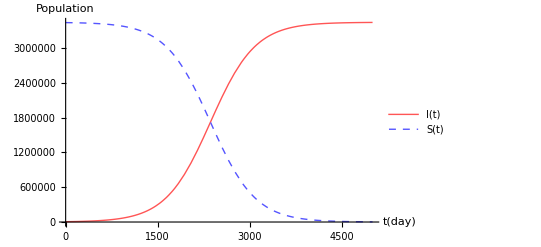

```mathematica
U[t_]:=(9248089730 *E^(0.002738514018463815t ))/(1718208+2687 *E^(0.002738514018463815t ))
n=3441790;
SetOptions[Plot,BaseStyle->{FontSize->16}];
Plot[{U[x],n-U[x]},{x,0,5000},PlotLegends->{"I(t)","S(t)",FontSize->30},AxesLabel->{"t(day)","Population",FontSize->20},PlotStyle->{{Lighter[Red],Thick},{Lighter[Blue],Dashed,Thick}}]
```

```mathematica
(* ==== Guinea ==== *)
ClearAll[b,x,u0,s0,S,U,data,ϵ];
n=10057975;(*modified*)

data = {2754,2784,2813,2828,2844,2859,2874,2890,2925,2959,2989,3019,3049,3079,3110,3143,3176,3195,3214,3233,3256,3256,3298,3322,3364,3405,3447,3463,3479,3535,3558,3583,3608,3633,3643,3652,3683,3714,3758,3801,3845,3891,3891,3944,3996,4024,4053,4081,4105,4106,4140,4174,4193,4213,4232,4252,4252,4263,4290,4298,4307,4315,4315,4328,4343,4354,4374,4394,4414,4415,4415,4421,4425,4438,4452,4465,4479,4479,4482,4488,4502,4516,4530,4552,4552,4568}
ϵ=Sum[(data[[i+1]]-data[[i]]-x*(n-data[[i]])*data[[i]]/n)^2,{i,Length@data-1}]
N@Minimize[ϵ,x]

n=10057975;(*modified*)
u= DSolve[{U'[t]==x*(n-U[t])*U[t]/n,(*modified*)U[0]==2754},{U[t]},t]
```

{19663.6,{x→0.00526372}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{U[t]→(27699663150 ⅇ^(t x))/(10055221+2754 ⅇ^(t x))}}

```mathematica
ClearAll[U]
U[t_]:=(27699663150 *E^(0.005263717163269015t ))/(10055221+2754 *E^(0.005263717163269015t ))
For[i=0,i<86,i++,Print[U[i]]]
```

```mathematica
N@Correlation[{2754,2784,2813,2828,2844,2859,2874,2890,2925,2959,2989,3019,3049,3079,3110,3143,3176,3195,3214,3233,3256,3256,3298,3322,3364,3405,3447,3463,3479,3535,3558,3583,3608,3633,3643,3652,3683,3714,3758,3801,3845,3891,3891,3944,3996,4024,4053,4081,4105,4106,4140,4174,4193,4213,4232,4252,4252,4263,4290,4298,4307,4315,4315,4328,4343,4354,4374,4394,4414,4415,4415,4421,4425,4438,4452,4465,4479,4479,4482,4488,4502,4516,4530,4552,4552,4568},{2754,2769,2783,2798,2813,2827,2842,2857,2872,2888,2903,2918,2934,2949,2965,2980,2996,3012,3028,3044,3060,3076,3092,3108,3125,3141,3158,3174,3191,3208,3225,3242,3259,3276,3294,3311,3328,3346,3364,3381,3399,3417,3435,3453,3472,3490,3508,3527,3545,3564,3583,3602,3621,3640,3659,3678,3698,3717,3737,3757,3776,3796,3816,3837,3857,3877,3898,3918,3939,3960,3980,4001,4023,4044,4065,4087,4108,4130,4152,4173,4195,4218,4240,4262,4285,4307}]
```

0.97384

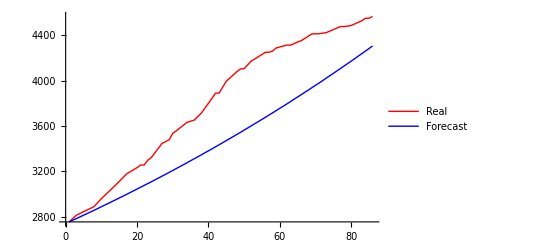

```mathematica
ListLinePlot[{{2754,2784,2813,2828,2844,2859,2874,2890,2925,2959,2989,3019,3049,3079,3110,3143,3176,3195,3214,3233,3256,3256,3298,3322,3364,3405,3447,3463,3479,3535,3558,3583,3608,3633,3643,3652,3683,3714,3758,3801,3845,3891,3891,3944,3996,4024,4053,4081,4105,4106,4140,4174,4193,4213,4232,4252,4252,4263,4290,4298,4307,4315,4315,4328,4343,4354,4374,4394,4414,4415,4415,4421,4425,4438,4452,4465,4479,4479,4482,4488,4502,4516,4530,4552,4552,4568},{2754,2769,2783,2798,2813,2827,2842,2857,2872,2888,2903,2918,2934,2949,2965,2980,2996,3012,3028,3044,3060,3076,3092,3108,3125,3141,3158,3174,3191,3208,3225,3242,3259,3276,3294,3311,3328,3346,3364,3381,3399,3417,3435,3453,3472,3490,3508,3527,3545,3564,3583,3602,3621,3640,3659,3678,3698,3717,3737,3757,3776,3796,3816,3837,3857,3877,3898,3918,3939,3960,3980,4001,4023,4044,4065,4087,4108,4130,4152,4173,4195,4218,4240,4262,4285,4307}},PlotStyle->{Red,Blue},PlotLegends->{"Real","Forecast"}]
```

```mathematica
(* ==== SLE ==== *)
ClearAll[b,x,u0,s0,S,U,data,ϵ];
n=6440053;(*modified*)

U = {5692,5781,5870,5957,6044,6132,6219,6306,6363,6419,6503,6587,6671,6755,6839,6949,7058,7159,7260,7361,7561,7561,7648,7861,7927,7993,8059,8101,8143,8314,8396,8488,8579,8671,8729,8787,9060,9333,9399,9465,9531,9599,9599,9707,9815,9896,9977,10058,10112,10112,10208,10303,10364,10424,10485,10545,10545,10736,10736,10762,10789,10815,10815,10848,10869,10908,10944,10979,11015,11048,11048,11062,11080,11106,11132,11158,11167,11167,11184,11205,11242,11279,11316,11335,11335,11349}
ϵ=Sum[(data[[i+1]]-data[[i]]-x*(n-data[[i]])*data[[i]]/n)^2,{i,Length@data-1}]
N@Minimize[ϵ,x]

u= DSolve[{U'[t]==x*(n-U[t])*U[t]/n,(*modified*)U[0]==5692},{U[t]},t]
```

{318018.,{x→0.00647473}}

{{U[t]→(36656781676 ⅇ^(t x))/(6434361+5692 ⅇ^(t x))}}

```mathematica
ClearAll[U]
U[t_]:=(36656781676 *E^(0.005263717163269015t ))/(6434361+5692 *E^(0.005263717163269015t ))
For[i=0,i<86,i++,Print[U[i]]]
```

```mathematica
N@Correlation[{5692,5781,5870,5957,6044,6132,6219,6306,6363,6419,6503,6587,6671,6755,6839,6949,7058,7159,7260,7361,7561,7561,7648,7861,7927,7993,8059,8101,8143,8314,8396,8488,8579,8671,8729,8787,9060,9333,9399,9465,9531,9599,9599,9707,9815,9896,9977,10058,10112,10112,10208,10303,10364,10424,10485,10545,10545,10736,10736,10762,10789,10815,10815,10848,10869,10908,10944,10979,11015,11048,11048,11062,11080,11106,11132,11158,11167,11167,11184,11205,11242,11279,11316,11335,11335,11349},{5692,5722,5752,5783,5813,5844,5874,5905,5937,5968,5999,6031,6063,6095,6127,6159,6192,6224,6257,6290,6323,6357,6390,6424,6458,6492,6526,6560,6595,6630,6665,6700,6735,6771,6806,6842,6878,6915,6951,6988,7024,7062,7099,7136,7174,7212,7250,7288,7326,7365,7404,7443,7482,7521,7561,7601,7641,7681,7722,7762,7803,7845,7886,7927,7969,8011,8053,8096,8139,8181,8225,8268,8312,8355,8399,8444,8488,8533,8578,8623,8669,8714,8760,8806,8853,8899}]
```

0.962911

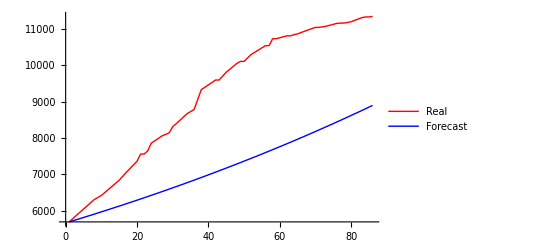

```mathematica
ListLinePlot[{{5692,5781,5870,5957,6044,6132,6219,6306,6363,6419,6503,6587,6671,6755,6839,6949,7058,7159,7260,7361,7561,7561,7648,7861,7927,7993,8059,8101,8143,8314,8396,8488,8579,8671,8729,8787,9060,9333,9399,9465,9531,9599,9599,9707,9815,9896,9977,10058,10112,10112,10208,10303,10364,10424,10485,10545,10545,10736,10736,10762,10789,10815,10815,10848,10869,10908,10944,10979,11015,11048,11048,11062,11080,11106,11132,11158,11167,11167,11184,11205,11242,11279,11316,11335,11335,11349},{5692,5722,5752,5783,5813,5844,5874,5905,5937,5968,5999,6031,6063,6095,6127,6159,6192,6224,6257,6290,6323,6357,6390,6424,6458,6492,6526,6560,6595,6630,6665,6700,6735,6771,6806,6842,6878,6915,6951,6988,7024,7062,7099,7136,7174,7212,7250,7288,7326,7365,7404,7443,7482,7521,7561,7601,7641,7681,7722,7762,7803,7845,7886,7927,7969,8011,8053,8096,8139,8181,8225,8268,8312,8355,8399,8444,8488,8533,8578,8623,8669,8714,8760,8806,8853,8899}},PlotStyle->{Red,Blue},PlotLegends->{"Real","Forecast"}]
```